```mathematica
w=20;
open="4.0";
extend="2.0";

prefix="D:\\Recovery\\Eclipse\\eclipse\\readme\\workspace\\NetworksFinalProject\\";
s1="AlignmentStats_NWGlobalAligner_CorrelationScoreFunction_2012_1_1_to_2013_1_1O_"<>open<>"_E_"<>extend<>"W_"<>ToString[w];
s2="network_NWGlobalAligner_CorrelationScoreFunction_2012_1_1_to_2013_1_1O_"<>open<>"_E_"<>extend<>"W_"<>ToString[w];
s3="offsets_NWGlobalAligner_CorrelationScoreFunction_2012_1_1_to_2013_1_1O_"<>open<>"_E_"<>extend<>"W_"<>ToString[w];
s4="sectors_NWGlobalAligner_CorrelationScoreFunction_2012_1_1_to_2013_1_1O_"<>open<>"_E_"<>extend<>"W_"<>ToString[w];
s5="vertexData_NWGlobalAligner_CorrelationScoreFunction_2012_1_1_to_2013_1_1O_"<>open<>"_E_"<>extend<>"W_"<>ToString[w];
```

```mathematica
s5
```

vertexData_NWGlobalAligner_CorrelationScoreFunction_2012_1_1_to_2013_1_1O_3.0_E_1.0W_20

201

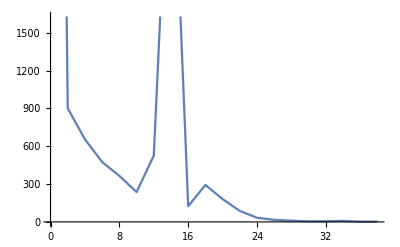

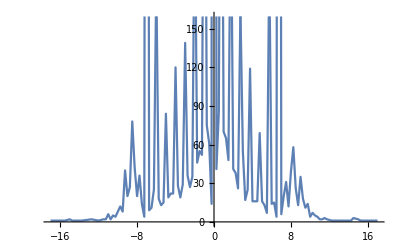

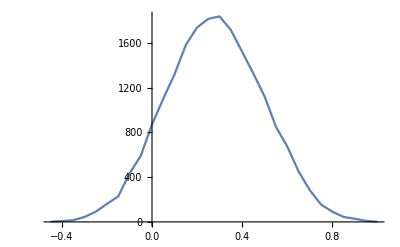

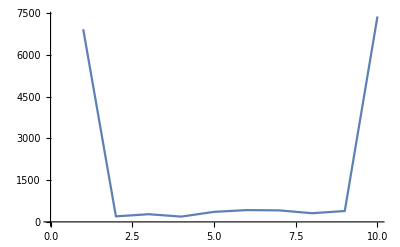

{{0,12697},{2,901},{4,655},{6,475},{8,365},{10,237},{12,526},{14,3477},{16,125},{18,293},{20,181},{22,87},{24,33},{26,16},{28,10},{30,5},{32,5},{34,8},{36,2},{38,2}}

{6925.,199.,276.,190.,361.,424.,414.,312.,391.,7386.}

```mathematica
alignmentStats=ToExpression[Import[prefix<>s1,"List"]];
temp=Import[prefix<>s2,"List"];
offsets=Import[prefix<>s3,"List"];
sectors=Import[prefix<>s4,"List"];
sectors=ToExpression[sectors[[1]]];
vertexDat=Import[prefix<>s5,"List"];


ts=ToString[temp[[1]]];
ts=StringReplace[ts,"{"->""];
ts=StringReplace[ts,"}"->""];
split=StringSplit[ts,","];



numVerts=Length[sectors]
network=Table[Table[ToExpression[split[[(i-1)*numVerts+j]]],{j,1,numVerts}],{i,1,numVerts}];

ts=ToString[offsets[[1]]];
ts=StringReplace[ts,"{"->""];
ts=StringReplace[ts,"}"->""];
split=StringSplit[ts,","];
offsets=Table[Table[ToExpression[split[[(i-1)*numVerts+j]]],{j,1,numVerts}],{i,1,numVerts}];

gapFreqs=alignmentStats[[1]];
offsetDist=alignmentStats[[2]];
scoreDist=alignmentStats[[3]];
gapOpenDist=alignmentStats[[4]];
toAdd=gapOpenDist[[Length[gapOpenDist]]];
gapOpenDist=gapOpenDist[[Range[10]]];
gapOpenDist[[Length[gapOpenDist]]]+=toAdd;
ListLinePlot[gapFreqs]
ListLinePlot[offsetDist]
ListLinePlot[scoreDist]
ListLinePlot[gapOpenDist]
gapFreqs
gapOpenDist
```

```mathematica
list={ToString[temp[[1]]]};
data={ToString[temp[[1]]]};
data=Map[StringTrim[#,("{"|"}")...]&,data];
data=Map[StringSplit[#,","]&,data];
data=StringTrim/@data;
Dimensions[data]
list2=StringTrim/@StringSplit[list,{"{",",","}"}];
Dimensions[list2]
```

{1,2601}

{1,2701}

```mathematica
Dimensions[data]
Dimensions[data[[1]]]
data[[1,51]]
```

{1,2601}

{2601}

0.08617211652719799}

```mathematica
sectors
```

```mathematica
temp=Import[prefix<>s3,"List"];
Dimensions[temp]
ts=ToString[temp[[1]]];
ts=StringReplace[ts,"{"->""];
ts=StringReplace[ts,"}"->""];
split=StringSplit[ts,","];
Dimensions[split]
ToExpression[split[[3]]]*ToExpression[split[[2]]]
```

{51}

{51}

-182.728

```mathematica
offsets[[1,2]]
offsets[[1,3]]
offsets[[2,3]]
```

-4.39442

-1.40637

0.615686

```mathematica
sets=Subsets[Range[10],{3}];
vals={};
For[i=1,i<Length[sets],i++,
s1=sets[[i,1]];
s2=sets[[i,2]];
s3=sets[[i,3]];
AppendTo[vals,{offsets[[s1,s2]],offsets[[s1,s3]],offsets[[s2,s3]]}];
]
```

```mathematica
vals
```

{{-1.43966,-1.76724,-5.84746},{-1.43966,0.,8.3431},{-1.43966,0.,0.},{-1.43966,0.,-8.74583},{-1.43966,0.,0.995671},{-1.43966,0.,8.159},{-1.43966,0.,0.},{-1.43966,0.,0.},{-1.76724,0.,0.995671},{-1.76724,0.,0.290043},{-1.76724,0.,-6.79325},{-1.76724,0.,6.79325},{-1.76724,0.,9.83402},{-1.76724,0.,0.},{-1.76724,0.,1.98276},{0.,0.,0.},{0.,0.,6.79325},{0.,0.,-8.65833},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.47619},{0.,0.,-6.79325},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.995671},{0.,0.,-6.79325},{0.,0.,-6.79325},{0.,0.,-0.995671},{0.,0.,-6.79325},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{-5.84746,8.3431,0.995671},{-5.84746,0.,0.290043},{-5.84746,-8.74583,-6.79325},{-5.84746,0.995671,6.79325},{-5.84746,8.159,9.83402},{-5.84746,0.,0.},{-5.84746,0.,1.98276},{8.3431,0.,0.},{8.3431,-8.74583,6.79325},{8.3431,0.995671,-8.65833},{8.3431,8.159,0.},{8.3431,0.,0.},{8.3431,0.,0.},{0.,-8.74583,0.},{0.,0.995671,0.47619},{0.,8.159,-6.79325},{0.,0.,0.},{0.,0.,0.},{-8.74583,0.995671,0.995671},{-8.74583,8.159,-6.79325},{-8.74583,0.,-6.79325},{-8.74583,0.,-0.995671},{0.995671,8.159,-6.79325},{0.995671,0.,0.},{0.995671,0.,0.},{8.159,0.,0.},{8.159,0.,0.},{0.,0.,0.},{0.995671,0.290043,0.},{0.995671,-6.79325,6.79325},{0.995671,6.79325,-8.65833},{0.995671,9.83402,0.},{0.995671,0.,0.},{0.995671,1.98276,0.},{0.290043,-6.79325,0.},{0.290043,6.79325,0.47619},{0.290043,9.83402,-6.79325},{0.290043,0.,0.},{0.290043,1.98276,0.},{-6.79325,6.79325,0.995671},{-6.79325,9.83402,-6.79325},{-6.79325,0.,-6.79325},{-6.79325,1.98276,-0.995671},{6.79325,9.83402,-6.79325},{6.79325,0.,0.},{6.79325,1.98276,0.},{9.83402,0.,0.},{9.83402,1.98276,0.},{0.,1.98276,0.},{0.,6.79325,0.},{0.,-8.65833,0.47619},{0.,0.,-6.79325},{0.,0.,0.},{0.,0.,0.},{6.79325,-8.65833,0.995671},{6.79325,0.,-6.79325},{6.79325,0.,-6.79325},{6.79325,0.,-0.995671},{-8.65833,0.,-6.79325},{-8.65833,0.,0.},{-8.65833,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.47619,0.995671},{0.,-6.79325,-6.79325},{0.,0.,-6.79325},{0.,0.,-0.995671},{0.47619,-6.79325,-6.79325},{0.47619,0.,0.},{0.47619,0.,0.},{-6.79325,0.,0.},{-6.79325,0.,0.},{0.,0.,0.},{0.995671,-6.79325,-6.79325},{0.995671,-6.79325,0.},{0.995671,-0.995671,0.},{-6.79325,-6.79325,0.},{-6.79325,-0.995671,0.},{-6.79325,-0.995671,0.},{-6.79325,0.,0.},{-6.79325,0.,0.},{0.,0.,0.}}

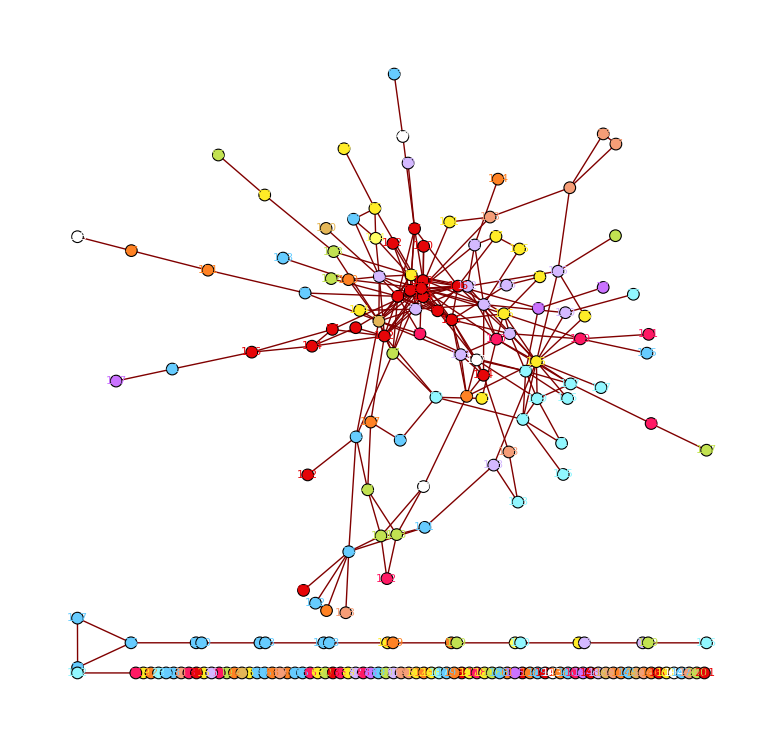

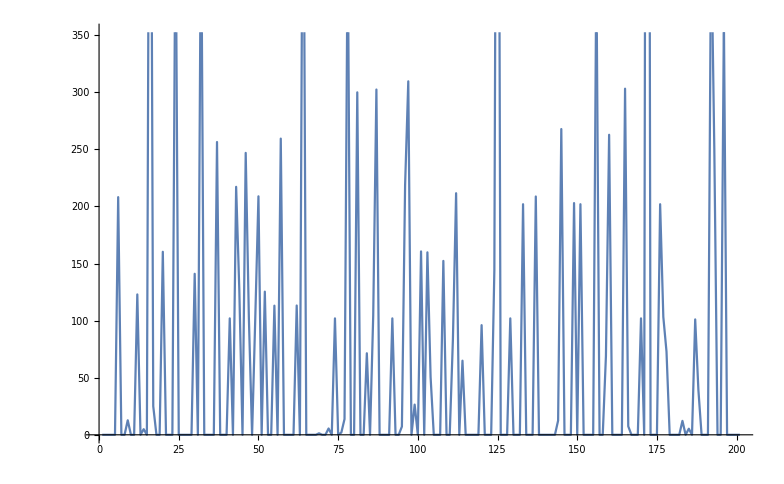

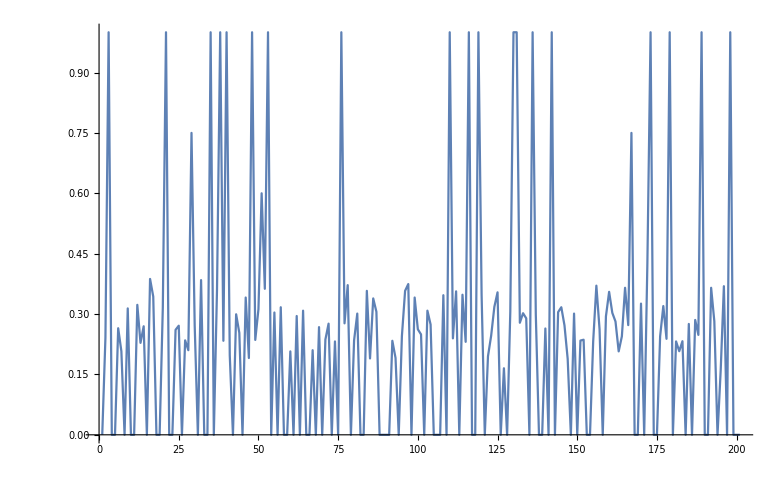

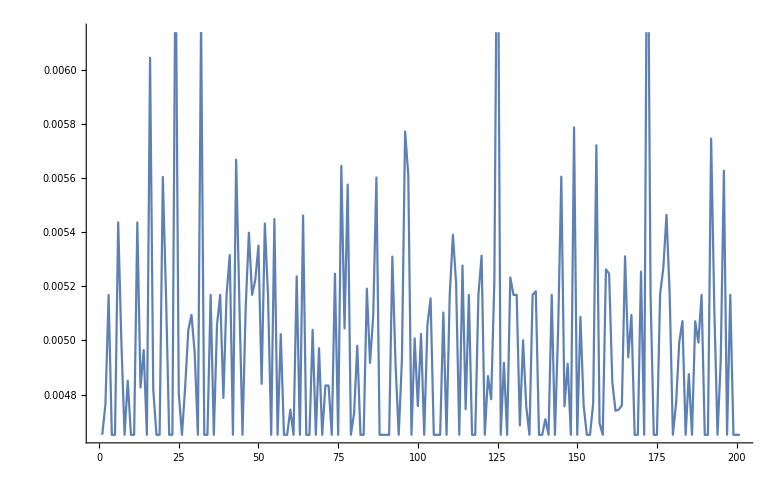

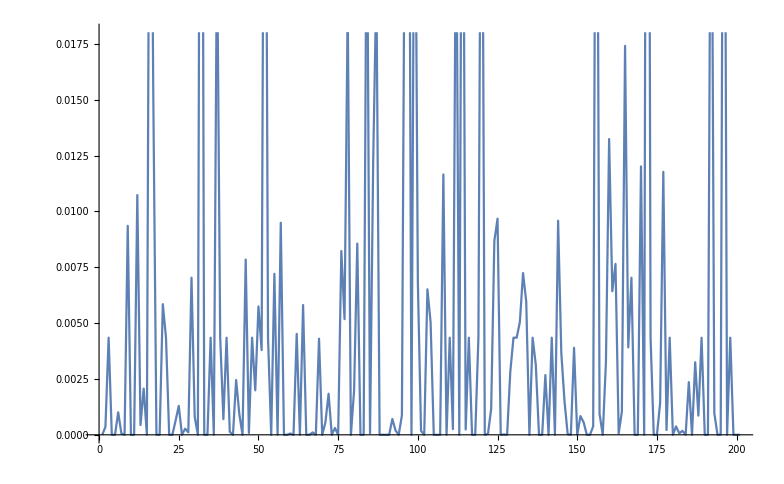

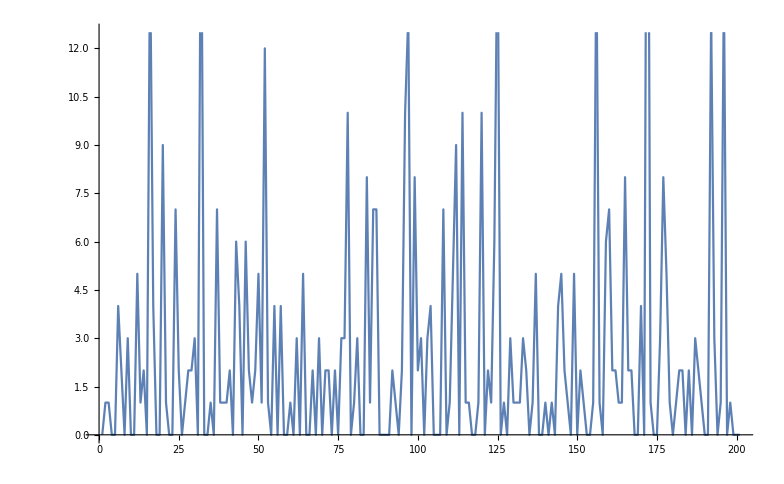

-Graphics-

```mathematica
t=0.45;
cd=ColorData[60,"ColorList"];
colors=Table[{i,cd[[sectors[[i]]]]},{i,1,Length[sectors]}];
GetNetwork[t_]:=AdjacencyGraph[Table[If[network[[i,j]]>t,1,0],{i,1,Length[network]},{j,1,Length[network]}]];
ShowNetwork[t_]:=GraphPlot[AdjacencyGraph[Table[If[network[[i,j]]>t,1,0],{i,1,Length[network]},{j,1,Length[network]}]],VertexRenderingFunction->({colors[[#2]][[2]],EdgeForm[Black],Disk[#,.1],colors[[#2]][[2]],Text[#2,#1]}&)];
ShowNetwork[t]
ListLinePlot[BetweennessCentrality[GetNetwork[t]]]
ListLinePlot[ClosenessCentrality[GetNetwork[t]]]
ListLinePlot[PageRankCentrality[GetNetwork[t],0.1]]
ListLinePlot[EigenvectorCentrality[GetNetwork[t]]]
ListLinePlot[DegreeCentrality[GetNetwork[t]]]

CommunityGraphPlot[GetNetwork[t],VertexLabels->Table[i->Style[ToString[sectors[[i]]],Black,Italic,18],{i,1,Length[sectors]}]]
```

{{13,14,20,27,43,46,62,71,74,86,108,115,124,125,129,137,146,147,149,155,157,159,160,165,166,177,181},{9,37,39,41,50,55,57,69,72,95,96,103,104,123,127,140,144,161,170,172,176,187,192},{12,16,17,32,52,77,78,80,84,87,97,99,100,112,114,120,132,134,156,162,164,185,196},{7,24,30,44,60,64,101,111,122,152,163,178,182,183,188,193},{2,6,25,28,67,145},{29,51,76,167},{47,81,151,195},{85,92,133},{3,110},{21,142},{35,48},{38,130},{40,119},{49,93},{53,189},{116,173},{131,198},{136,179},{1},{4},{5},{8},{10},{11},{15},{18},{19},{22},{23},{26},{31},{33},{34},{36},{42},{45},{54},{56},{58},{59},{61},{63},{65},{66},{68},{70},{73},{75},{79},{82},{83},{88},{89},{90},{91},{94},{98},{102},{105},{106},{107},{109},{113},{117},{118},{121},{126},{128},{135},{138},{139},{141},{143},{148},{150},{153},{154},{158},{168},{169},{171},{174},{175},{180},{184},{186},{190},{191},{194},{197},{199},{200},{201}}

{{10,5,4,4,4,3,10,4,12,2,2,4,1,5,2,4,4,7,12,8,4,4,12,5,2,6,12},{1,7,5,8,4,5,1,8,5,8,2,9,1,8,10,11,13,5,3,1,1,3,1},{2,11,12,1,1,5,2,2,2,1,5,1,1,2,1,1,7,5,1,1,3,5,1},{3,8,6,7,1,8,8,7,12,1,9,7,8,4,9,2},{7,9,5,9,9,2},{8,8,8,8},{3,8,3,6},{7,5,7},{8,8},{12,4},{2,2},{5,4},{13,7},{6,8},{3,3},{8,8},{5,8},{4,7},{1},{1},{3},{5},{7},{12},{5},{8},{5},{3},{4},{8},{9},{12},{1},{2},{3},{11},{8},{8},{3},{9},{3},{8},{8},{12},{5},{7},{1},{12},{5},{2},{12},{10},{8},{7},{2},{9},{9},{5},{3},{5},{4},{8},{3},{5},{12},{5},{7},{8},{10},{3},{8},{1},{6},{3},{8},{12},{10},{1},{2},{11},{9},{3},{8},{11},{9},{3},{1},{5},{6},{8},{9},{7},{1}}

{{{10,2},{5,3},{4,9},{3,1},{12,4},{2,4},{1,1},{7,1},{8,1},{6,1}},{{1,6},{7,1},{5,4},{8,4},{4,1},{2,1},{9,1},{10,1},{11,1},{13,1},{3,2}},{{2,5},{11,1},{12,1},{1,10},{5,4},{7,1},{3,1}},{{3,1},{8,4},{6,1},{7,3},{1,2},{12,1},{9,2},{4,1},{2,1}},{{7,1},{9,3},{5,1},{2,1}},{{8,4}},{{3,2},{8,1},{6,1}},{{7,2},{5,1}},{{8,2}},{{12,1},{4,1}},{{2,2}},{{5,1},{4,1}},{{13,1},{7,1}},{{6,1},{8,1}},{{3,2}},{{8,2}},{{5,1},{8,1}},{{4,1},{7,1}},{{1,1}},{{1,1}},{{3,1}},{{5,1}},{{7,1}},{{12,1}},{{5,1}},{{8,1}},{{5,1}},{{3,1}},{{4,1}},{{8,1}},{{9,1}},{{12,1}},{{1,1}},{{2,1}},{{3,1}},{{11,1}},{{8,1}},{{8,1}},{{3,1}},{{9,1}},{{3,1}},{{8,1}},{{8,1}},{{12,1}},{{5,1}},{{7,1}},{{1,1}},{{12,1}},{{5,1}},{{2,1}},{{12,1}},{{10,1}},{{8,1}},{{7,1}},{{2,1}},{{9,1}},{{9,1}},{{5,1}},{{3,1}},{{5,1}},{{4,1}},{{8,1}},{{3,1}},{{5,1}},{{12,1}},{{5,1}},{{7,1}},{{8,1}},{{10,1}},{{3,1}},{{8,1}},{{1,1}},{{6,1}},{{3,1}},{{8,1}},{{12,1}},{{10,1}},{{1,1}},{{2,1}},{{11,1}},{{9,1}},{{3,1}},{{8,1}},{{11,1}},{{9,1}},{{3,1}},{{1,1}},{{5,1}},{{6,1}},{{8,1}},{{9,1}},{{7,1}},{{1,1}}}

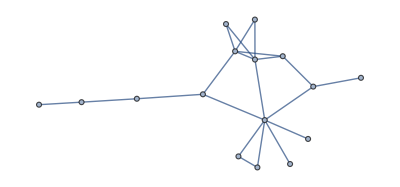

```mathematica
comms=FindGraphCommunities[GetNetwork[t]]
secs=Table[Table[sectors[[comms[[i,j]]]],{j,1,Length[comms[[i]]]}],{i,1,Length[comms]}]
tallied=Map[Tally,secs]
Subgraph[GetNetwork[t],comms[[4]]]
```

{10,5,4,4,4,3,10,4,12,2,2,4,1,5,2,4,4,7,12,8,4,4,12,5,2,6,12}

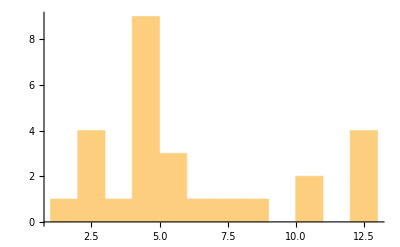

```mathematica
secs[[1]]
Histogram[secs[[1]],12,"Count"]
```

```mathematica
ssets=Subsets[Range[200],{2}];
Select[Table[offsets[[ssets[[i,1]],ssets[[i,2]]]]*If[network[[ssets[[i,1]],ssets[[i,2]]]]>t,1,0],{i,1,Length[ssets]}],Positive]
Select[Table[offsets[[ssets[[i,1]],ssets[[i,2]]]]*If[network[[ssets[[i,1]],ssets[[i,2]]]]>t,1,0],{i,1,Length[ssets]}],Negative]
Table[offsets[[ssets[[i,1]],ssets[[i,2]]]]*If[network[[ssets[[i,1]],ssets[[i,2]]]]>t,1,0],{i,1,Length[ssets]}];
Table[If[network[[ssets[[i,1]],ssets[[i,2]]]]>t,network[[ssets[[i,1]],ssets[[i,2]]]],0],{i,1,Length[ssets]}];
```

{0.637931,6.79325,8.42678,0.294372,4.89362}

{-8.37657,-6.79325,-11.9098,-6.79325,-0.995671}

```mathematica
Subgraph[GetNetwork[t],comms[[4]]]
```

```mathematica
offsets[[5]];
```

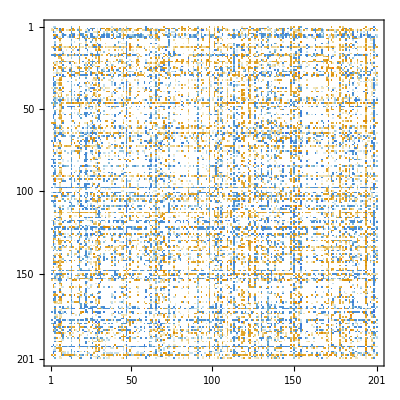

{{17.2129,1},{16.9076,1},{15.6895,1},{15.4656,1},{15.3644,1},{15.0607,1},{15.0202,1},{14.8862,1},{14.875,1},2730,{-14.8862,1},{-15.0202,1},{-15.0607,1},{-15.3644,1},{-15.4656,1},{-15.6895,1},{-16.9076,1},{-17.2129,1}}
 |  |  |  |

```mathematica
MatrixPlot[offsets]
Sort[Tally[Flatten[offsets]],#1[[1]]>#2[[1]]&]
```

```mathematica
scoreDist
```

{{-5.1,1},{-0.05,3},{0.,62},{0.05,63},{0.1,81},{0.15,98},{0.2,104},{0.25,126},{0.3,117},{0.35,114},{0.4,98},{0.45,83},{0.5,77},{0.55,52},{0.6,36},{0.65,27},{0.7,17},{0.75,5},{0.8,7},{0.85,4},{1.,1}}

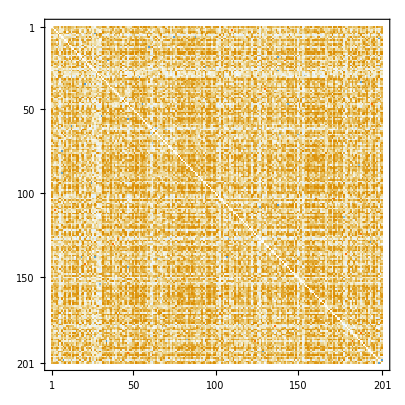

```mathematica
MatrixPlot[network]
```

```mathematica
Sort[Tally[Flatten[network]],#1[[1]]>#2[[1]]&]
```

{{20.3165,2},{19.6667,2},{18.8363,2},{18.3718,2},{17.5914,2},{14.4314,2},{13.5017,2},{11.6035,2},20085,{-23.705,2},{-25.0191,2},{-25.2546,2},{-26.3495,2},{-27.1033,2},{-27.3394,2},{-27.9845,2},{-28.1572,2}}
 |  |  |  |